# Epidemiology

## A Network Analysis Overview

Titonis Tryfon

Postgraduate Student

Aristoteleio University of Thessaloniki
Faculty of Physical Sciences
Department of Physics

25/4/2017

Introduction

Epidemiology is the study of the distribution and determinants of health-related states or events (including disease), and the application of this study to the control of diseases and other health problems^[].

The study of epidemiology has begun with the Greek physician Hippocrates, who first tried to figure out the relationship between occurrences of disease and outside influences. As a scientific study, as we understand it today, epidemiology though has been established during the middle ages and later, especially after the capability to observe and identify microorganisms has been developed.

There are three main types of studies used in epidemiology, descriptive studies, analytical studies, and experimental studies^[].

The first type, the descriptive, or surveillance studies, can be used to study distribution. Nature is allowed to “take its course”, and observations are made during that period, without any attempt to tamper or drive the events.

Analytical studies are instead used to study determinants. They are mostly theoretical in nature.

The last type, the experimental studies are where the scientist takes control of the event.

The Bradford Hill criteria are used to determine causality in Epidemiology. Although, according to their author, “none of them can bring indisputable evidence for or against the cause-of-effect hypothesis and none can be be required sina qua non”^[].

The purpose of epidemiology is many-fold. Firstly, epidemiological studies can be used to effectively use population based health management. Another use is assessment of threatening conditions that emerge from time to time. And most importantly, epidemiology provides as with the ability to predict outbreaks that may happen before even they begin.

In this work the types of networks used in epidemiology are reviewed at first, as also some general graph theory used in epidemiological studies. Then, it is attempted to create a network with such characteristics, and to study how an epidemic happens in such a network. The focus will be placed mostly on determining the characteristics of the network, and if this application ensues the theory about the disease thresholds in a network.

Networks & Graphs

Network/Graph Theory

Definitions^[]

A network or a graph (G) - both names will be used interchangeably - is a structure composed of sets of nodes (V) and sets of edges (E) which link the nodes. Usually, links are established only between pairs of nodes. Either one of these sets (V & E) or both also have some attributes associated with them, depending on what the network is designed to describe.

G=<V,E>

A network can be described by its adjacency matrix:

A_ij={a_ij}

Its rows and columns define the nodes, while its elements correspond to the edges, or links between the nodes. An entry of zero defines that there is no connection between the corresponding nodes, while a non-zero entry defines a link.

We can split the networks into two major types, depending on their link values; those that have entries of 1 only, and those that have a real number as a link value (0,1]. The latter contain weighted links, while in the former all links are of equal value.

Furthermore, the graphs can be identified as directed or undirected. Links on the former type define only one-way connection, allowing “movement” from a specific node to another, but not back. The undirected feature two-way links. Undirected graphs are described by a symmetrical adjacency matrix (on the main diagonal).

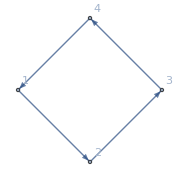
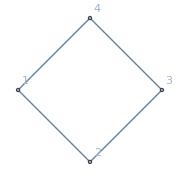
directed graph
 | 1 | 2 | 3 | 4
1 | 0 | 1 | 0 | 0
2 | 0 | 0 | 1 | 0
3 | 0 | 0 | 0 | 1
4 | 1 | 0 | 0 | 0
-Graphics-undirected graph
 | 1 | 2 | 3 | 4
1 | 0 | 1 | 0 | 1
2 | 1 | 0 | 1 | 0
3 | 0 | 1 | 0 | 1
4 | 1 | 0 | 1 | 0
-Graphics-

```mathematica
ClearAll["Global`*"]
Row[{
Column[{
b={{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}};
Style["directed graph",Italic],
TableForm[b,TableHeadings->{Range[4],Range[4]}],
AdjacencyGraph[b,VertexLabels->"Name",ImageSize->Small]
},Alignment->Center,Spacings->0.5]
,
Column[{
a={{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}};
Style["undirected graph",Italic],
TableForm[a,TableHeadings->{Range[4],Range[4]}],
AdjacencyGraph[a,VertexLabels->"Name",ImageSize->Small]
},Alignment->Center,Spacings->0.5]
},Spacer[50]]
```

Topology^[]

To better define and describe a network we need to describe and measure its properties and topology. To this purpose, a number of properties has been defined.

Degree (k_i)

We define degree of a node the number of edges connected to it.

k_i=∑_(j=1)^N a_ij (if a_ij>0)

Degree Distribution

A network’s degree distribution is the distribution that gives the probability each node has a certain number of links (degree). It has been discovered that most realistic networks differ from a Poisson distribution, and instead they exhibit a tail that follows a power law distribution.

Neighbors

Neighbors of a node are the nodes at the other sides of the edges connecting to the node.

Path

As a path within a graph we define a sequence of nodes {v_i,v_2,...,v_n}, where adjacent pairs of nodes are connected with an edge. For directed graphs, the connection needs to point from the former node to the later.

Path Length

A path’s length is the number of nodes contained in it minus one.

Characteristic Path Length

The characteristic path length is defined as the median of the means of the shortest path lengths connecting each vertex to all other vertices.

L=1/N∑_(i=1)^N L_i=1/N∑_(i=1)^N (∑_(j=1,i≠j)^N d_ij)/(N-1)

Cycle

We call any path that starts and ends on the same node a cycle.

Connectivity

A graph is considered connected if all of its nodes appear on at least one path. If there is a node not connected to any path, then the graph is called disconnected.

Distance

Distance between two nodes in a graph is defined as the length of the shortest path between those two nodes.

Diameter

We define the diameter of a graph as the maximum distance between any pair of its nodes.

A disconnected path features an infinite diameter.

Regular Network

A regular network appears when all of its nodes have the same number of neighbors.

Tree

A tree is a connected graph that does not contain any cycles among its paths.

Clustering Coefficient

The clustering coefficient is a measure of the tendency of nodes in a graph to form clusters. It is given as the ration between the number of edges that actually exist between k_i nodes (E_i) and the total number of edges that could appear ((k_i(k_i-1))/2) between those nodes.

C_i=(2 E_i)/(k_i(k_i-1))

Network Density

Similar to the clustering coefficient, but on a global scale, the network density is defined as the ration between the number of edges appearing in a graph and the total number of edges that could appear in the same graph.

Assortative Mixing

Assortative mixing refers to the correlations between properties of adjacent nodes. It can be represented in terms of node degrees.

Assortativity takes values in the range of [-1,1], with 1 meaning that the nodes tend to link with nodes with of similar degree. The high assortativity of realistic networks is what creates the communities that appear.

Complex Networks

A network is considered complex when in it occur non-trivial topological features; ones that do not occur in simple networks but only in graphs modelling real systems.

Such features are used to measure a network’s complexity, and include a heavy tail in the degree distribution, a high clustering coefficient, assortativity or lack of it, communities, or an hierarchical structure.

Small World Network

The idea of the small world network is that in a realistic network, despite its huge size, there is a relatively short path between any two nodes. This has been made famous by the “six degrees of separation”; the fact that in the real world any two people are only six edges afar, regardless of their location on the world. This property appears to characterize most complex networks.

A measure of ‘small-world-ness’ S^[] is proposed:

S=(C/C_rand)/(L/L_rand)

where C is the clustering coefficient of the network, L the characteristic path length of the network, and the index rand refers to a random network of the same size.

A small world network exhibits a high cluster coefficient and a small path length.

Scale-Free Network

A scale-free network is one that its degree distribution follows a power law, at least asymptotically.

P(k)~k^-γ

It is considered that this property is derived from the preferential attachment of nodes.

The most common characteristic of scale-free networks is the appearance of “hubs”, which are nodes with a degree much higher than the average degree of the network.

Communities

In a network, sets of nodes that are well connected among themselves but appear to have limited connections to other nodes in the network are called communities.

Loosely, we identify a community as a set of nodes that exhibit more connections among themselves than the total of their connections to nodes outside of the community.

Epidemiology

The SIR Model

Epidemiology started with the study of a simplified system, the SIR. This model has been augmented by researchers throughout the years to better describe epidemic dynamics, but regardless of its simplicity it remains one of the best tools to begin with.

The model considers that the population is divided into three groups, the Susceptible, the Infected, and the Removed. The infected are the ones already carrying the disease, the susceptible are the ones that do not have the disease but may contract it, while the removed are the ones that do not have the disease and cannot contract it. When adapting the model to a specific disease the connections between those groups must be defined, and then, through those connections the dynamics of the system can be determined.

The SIR model describes accurately one of the two main kinds of infection: the common source infection. This kind of infection is a random occurrence that belongs to a Poisson distribution^[]. The second kind of infection, the propagated infection, can be better described with a scale-free network^[].

Graph Theory for Epidemiology

The usual method for studying epidemiology in a population is through the dynamics described by a set of differential equations (stochastic method). This approach, although it shows results, has a major flaw; the assumption that each individual has the ability to transmit something (a disease in our case) to the same number of individuals within the population. In a realistic description of the world this does not hold true, instead each individual can transmit only to a limited set of others, who are connected with the individual somehow. This effect can be implemented into a model easily through the use of graphs; where each individual, or node in the graph, has the ability to transmit to only some others, the node’s neighbors.

Furthermore, graph theory becomes a powerful tool, allowing us to avoid extensive, time consuming simulations needed when solving such a complex dynamic system.

The power law distribution that describes certain networks, especially the scale-free networks, seems to fit the distribution of epidemics^[].

The SIR(S) Model Revisited

When applying graph theory in the study of epidemiology we need to redefine the SIR model.

For a population N, consider that an infected individual i makes local infectious contacts with j individual at a rate λ_ij^L and global contacts at a rate of λ_G (individual to individual global infection rate λ_G/N). If a contacted individual is still susceptible, then it becomes infected and is immediately able to infect others. If a contacted individual is already infected or belongs to the removed group, then nothing happens. An infected individual can either change to a removed or a susceptible after a specific time.

Small World Network

The small world network can be described as a network of unsocial inhabitants occupying a village-like location, where contact is limited to neighbors^[].

Great Circle Network

This network considers that individuals do not belong to local clumps, or households, but they are instead distributed on an one-dimensional space, forming connections to their closest (one or more) neighbors.

Scale-Free Network

As mentioned before, a scale-free network is a network that contains hubs with connectivity distribution based on the power-law distribution. Most of the nodes have only a few connections, but a few nodes appear to have many connections^[]. The distribution P(k) of such a model can be written as^[]:

P(k)=Piecewise[{{(k-1)/(k+2)P(k-1),, k≥m+1}, {2/(m+2),, k=m}}]

where k is the connectivity and m is the connection degree of new and old nodes.

SHEM (Spatial Hierarchical Epidemic Model)

One quite complex network that retains some simplicity for calculations is the SHEM model. This model exhibits many of the previous models’ properties, i.e. spatial features, power law distribution of connectivity, and also possesses a community structure with transmission rates between two individuals depending on the communities to which they both belong.

Mixing Levels

Mixing levels in epidemiology is introduced to better describe heterogeneity in a population^[]. The simplest model with mixing assumes that an individual has only a global probability p_G of infecting each other individual in the population and a local probability p_L of infecting its neighbors. It is usually p_L>>p_G.

This type of mixing can describe adequately human epidemics, where close socialization, in ones home, school, or work, introduces a greater risk of infection than from a random stranger that one comes in contact casually^[].

Outbreaks

When we introduce time dependency on the model we can observe the appearance of non-periodic outbreaks^[]. This approach also requires that the nodes of the network are not static, that they actually change their connections, both in number and in distance, over time. Another requirement to observe both periodic and non-periodic outbreaks is the existence of persistent epidemic seeds. Thus, to describe such effects, the SIRS model is better used.

Model Description

Sets and Parameters

N: total population

R: Threshold parameter

In a two-level mixing epidemics model, a large outbreak will be possible if R>1, where R=R_G·μ, with R_G the reproductive ration for global contacts and μ the mean size of outbreaks utilizing only local contacts^[].

p: infection probability

The global infection probability is assumed to be equal for all individuals, and related to the size of the population. This holds true in most cases, although it will need to be adjusted if vaccination is introduced to the population. In this study, it is considered that there will be no vaccination strategy though.

p_G~N^-1

p_L

T_i: The length of time an individual is infected and thus is infectious, is considered to follow a Poisson distribution.

Creating a Realistic Network

Models

During the years many models have been proposed and were used to create random, realistic networks. Examples of such models are the following:

Erdos-Renyi (ER) random network model

To construct such a network generate N nodes in space and then connect any two nodes with a predetermined probability p.

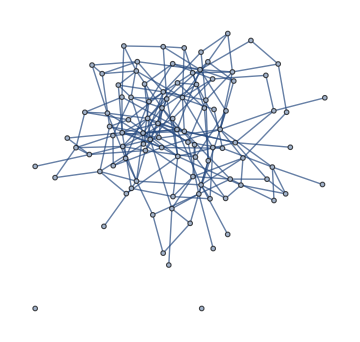
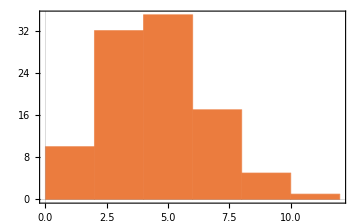
Erdos-Renyi Network
Population: 100, Link chance: 0.05
-Graphics-
Degree Distribution
-Graphics-

```mathematica
NErdosRenyi=100;
pErdosRenyi=0.05;
aErdosRenyi=Table[0,{NErdosRenyi},{NErdosRenyi}];
For[i1=1,i1≤NErdosRenyi,i1++,
For[i2=i1+1,i2≤NErdosRenyi-1,i2++,
If[RandomReal[]≤pErdosRenyi,
aErdosRenyi[[i1,i2]]=1;
aErdosRenyi[[i2,i1]]=1;
]
]
]
Column[{
Style["Erdos-Renyi Network",{Bold,Large}],
StringForm["Population: ``, Link chance: ``",NErdosRenyi,pErdosRenyi],
graphErdosRenyi=AdjacencyGraph[aErdosRenyi,ImageSize->Medium],
Style["Degree Distribution",Italic],
Histogram[VertexDegree[graphErdosRenyi],ImageSize->Medium,PlotTheme->"Scientific"]
},Alignment->Center]
```

Watts-Stogatz small world network

Create a ring lattice with N nodes connected to their first 2M neighbors (M on either side), with N>>M>>ln(N)>>1. Then randomly rewire each edge of the lattice with probability p such that self-connections and duplicate edges are excluded.

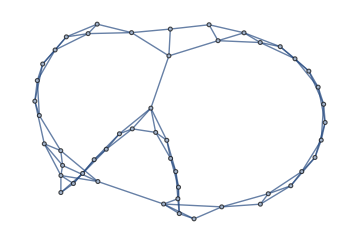
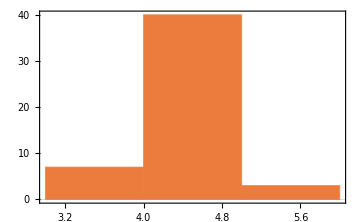
Watts-Stogatz Small World Network
Population: 50, Local connections: 2
-Graphics-
Degree Distribution
-Graphics-

```mathematica
NWattsStogatz=50;
pWattsStogatz=0.02;
mWattsStogatz=2;
aWattsStogatz=Table[0,{NWattsStogatz},{NWattsStogatz}];
(*step 1:create the circle network with m-neighbors*)
For[i=1,i≤NWattsStogatz,i++,
For[j=1,j≤NWattsStogatz,j++,
If[Or[
And[j≥i+1,j≤i+mWattsStogatz],
And[i≥j+1,i≤j+mWattsStogatz],
And[i≥NWattsStogatz+1-mWattsStogatz,i≤NWattsStogatz,j≥1,j≤mWattsStogatz,NWattsStogatz-i+j≤mWattsStogatz],
And[j≥NWattsStogatz+1-mWattsStogatz,j≤NWattsStogatz,i≥1,i≤mWattsStogatz,NWattsStogatz-j+i≤mWattsStogatz]
],
aWattsStogatz[[i,j]]=1;aWattsStogatz[[j,i]]=1;
];
]
];
(*step 2:randomly move some connections*)
For[i=1,i≤NWattsStogatz,i++,
For[j=1,j≤NWattsStogatz,j++,
If[And[aWattsStogatz[[i,j]]==1,RandomReal[]≤pWattsStogatz],
aWattsStogatz[[i,j]]=0;aWattsStogatz[[j,i]]=0;
If[RandomReal[]≤0.5,
(*change on row*)k=RandomChoice[Complement[Range[NWattsStogatz],{j}]];aWattsStogatz[[k,j]]=1;aWattsStogatz[[j,k]]=1;,
(*change on column*)k=RandomChoice[Complement[Range[NWattsStogatz],{i}]];aWattsStogatz[[i,k]]=1;aWattsStogatz[[k,i]]=1;
]
];
]
];
Column[{
Style["Watts-Stogatz Small World Network",{Bold,Large}],
StringForm["Population: ``, Local connections: ``",NWattsStogatz,mWattsStogatz],
graphWattsStogatz=AdjacencyGraph[aWattsStogatz,ImageSize->Medium],
Style["Degree Distribution",Italic],
Histogram[VertexDegree[graphWattsStogatz],ImageSize->Medium,PlotTheme->"Scientific"]
},Alignment->Center]
```

Barabasi-Albert scale-free network

Starting with a small number of connected nodes (m_0), at every time step, we add a new node with m edges (m<m_0) that link the new node to m different existing nodes. The probability of each new connection increases with the number of connections the target node already has.

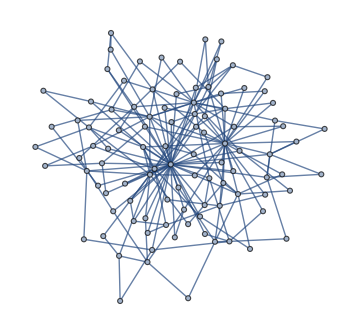
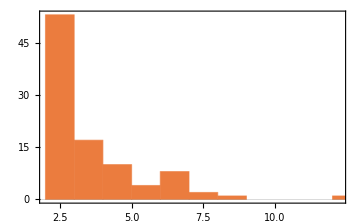
Barabasi-Albert Scale-Free Network
-Graphics-
Degree Distribution
-Graphics-

```mathematica
Column[{
Style["Barabasi-Albert Scale-Free Network",{Bold,Large}],
graphBarabasiAlbert=RandomGraph[BarabasiAlbertGraphDistribution[100,2],ImageSize->Medium],
Style["Degree Distribution",Italic],
Histogram[VertexDegree[graphBarabasiAlbert],ImageSize->Medium,PlotTheme->"Scientific"]
},Alignment->Center]
```

SHEM network^[]

Consider a set V whose elements represent either individuals or their fixed positions, and the set B of all edges between them. Then consider a set B_1⊆B of basic edges that determine the basic graph. Next, take a hierarchical structure of partitions of V into larger blocks representing communities. Then consider random sets S of communities to which individuals belong.

Two individuals are considered to be in contact if they are linked with a basic edge or if they are members of the same community.

Network Creation

An attempt to create a random but realistic network that exhibits all the above properties is made based on the method of creation for a SHEM network.

First, the number of communities within that population is defined. The size of each community is determined randomly, based on the χ^2 distribution. This results in a many small communities (households, offices) a few larger ones (schools, factories, etc), even fewer individuals or extremely small communities, and a total population of approximately the number of communities squared.

Then, the connections of each individual is determined randomly. Each individual is taken to make local connections in his community based on a poison distribution with a mean equal to one third of the community’s size. Based on the number of connections, adjacency matrices are created for each community. These matrices are then joined so as to form a diagonal matrix with these on its diagonal.

The next step is the creation of inter-community links, based on a fixed probability. By keeping the communities isolated (small chance for an inter-community link), we observe that the degree distribution exhibits the power-law distribution’s tail, but the low-degree nodes are fewer than in a scale-free network.

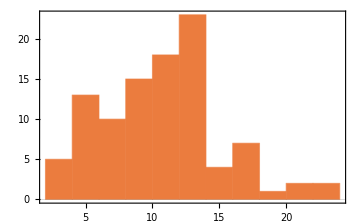
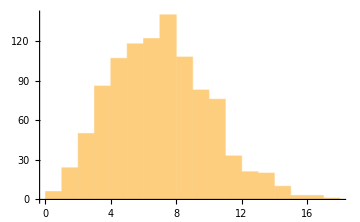
Test Network
Population: 1011, Communities: 100
Community sizes
-Graphics-
Degree Distribution
-Graphics-

```mathematica
Column[{
(*basic community and population data*)
Ncommunities=100;
communitySize=Floor[RandomVariate[ChiSquareDistribution[10],Ncommunities]];
Ntotal=Total[communitySize];
Style["Test Network",{Bold,Large}],
StringForm["Population: ``, Communities: ``",Ntotal,Ncommunities],
Style["Community sizes",Italic],
Histogram[communitySize,ImageSize->Medium,PlotTheme->"Scientific"],

(*create community links*)
communityLocalLinksMean=Floor[communitySize/4]/.{0->1};
A={};
For[i=1,i≤Ncommunities,i++,
links=Total[RandomVariate[PoissonDistribution[communityLocalLinksMean[[i]]],communitySize[[i]]]];
a=Table[0,{communitySize[[i]]},{communitySize[[i]]}];
linkPosa=RandomSample[Flatten[Table[{i,j},{i,1,Length[a]},{j,i+1,Length[a]}],1],UpTo[links]];
linkPosb=Map[Sort[#,Greater]&,linkPosa];
(a[[##]]=1)&@@#&~Scan~Join[linkPosa,linkPosb];
AppendTo[A,a];
];

(*create the adjacency matrix containing the above communities*)
Agraph=Fold[ArrayFlatten[{{#,-1},{-1,#2}}]&,A[[1]],A[[2;;-1]]];
pInterCommunity=0.001;
For[i=1,i≤Ntotal,i++,
For[j=i,j≤Ntotal,j++,
If[Agraph[[i,j]]==-1,
If[RandomReal[]<pInterCommunity,
Agraph[[i,j]]=1;
Agraph[[j,i]]=1;,
Agraph[[i,j]]=0;
Agraph[[j,i]]=0;
]

]
]
];
AgraphInit=Agraph;
graph=AdjacencyGraph[Agraph,ImageSize->Large];
Style["Degree Distribution",Italic],
Histogram[VertexDegree[graph],ImageSize->Medium]

},Alignment->Center]
```

Application

The test network created above will be used to study the spread of an infectious disease in such a population.

We consider that the disease can be transmitted only through contact, so only individuals connected directly with a link has a chance to get the diseases. Furthermore, there is a global infection chance for each individual, which is independent of the number of connections the individual has. For simplicity, we consider that the local connection chance of infection is also a set possibility.

The global infection chance for each time step is defined as p_G=N^-1. The local infection chance should be defined by the disease, and this study is considered as to be 0.5 for a highly contagious disease, like influenza.

An infected individual is taken to be infectious for a number of days based on a Poisson distribution with a mean of 10 days. At the end of this period the individual is either taken to the recovered group (chance of 0.1) which is immune to the disease or the susceptible group. This choice is made for a mild, non-persistent disease.

Initially, we consider that only 10 individuals are infected, and that those are spread randomly along the population. Afterwards, we run a simulation with a time step of 1 day. First, we want to check if by retaining the connections static we can achieve the results of the analytical SIRS model.

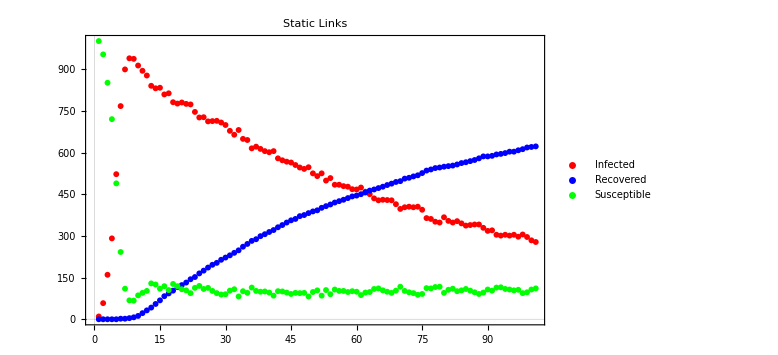

```mathematica
Agraph=AgraphInit;
pG=N[1/Ntotal];
pL=0.5;
T=10;
tmax=100;
state=Association[Apply[Sequence,Table[Rule[i,"susceptible"],{i,1,Ntotal}]]];
infectionTime=Association[Apply[Sequence,Table[Rule[i,0],{i,1,Ntotal}]]];
infectionTimeTotal=infectionTime;

(*initial infection*)
initialInfectionSize=10;
init=RandomSample[Range[Ntotal],initialInfectionSize];
For[i=1,i≤initialInfectionSize,i++,
state[init[[i]]]="infected";infectionTime[init[[i]]]=1;infectionTimeTotal[init[[i]]]=RandomVariate[PoissonDistribution[T]];]
Ninfected={initialInfectionSize};Nrecovered={0};

(*time loop*)
res=Reap@Do[
stateTemp=state;

For[i=1,i<Ntotal,i++,
(*increase infected time*)
If[infectionTime[i]>0,infectionTime[i]=infectionTime[i]+1];

(*if infected, infect others that are directly linked*)
If[state[i]=="infected",
For[j=1,j<Ntotal,j++
If[And[Agraph[[i,j]]>0,RandomReal[]≤pL,state[j]=="susceptible"],
stateTemp[j]="infected";
infectionTime[j]=1;
infectionTimeTotal[j]=RandomVariate[PoissonDistribution[T]];
]
]
];

(*global infection chance*)
If[And[state[i]=="susceptible",RandomReal[]≤pG],
stateTemp[i]="infected";
infectionTime[i]=1;
infectionTimeTotal[i]=RandomVariate[PoissonDistribution[T]];
];

];
state=stateTemp;

(*remove from infected with end of time*)
For[i=1,i<Ntotal,i++,
(*increase infected time*)
If[And[state[i]=="infected",infectionTime[i]≥infectionTimeTotal[i]],
If[RandomReal[]≤0.1,
state[i]="recovered";infectionTime[i]=0;infectionTimeTotal[i]=0;,
state[i]="susceptible";infectionTime[i]=0;infectionTimeTotal[i]=0;
]
];
];

(*counters*)
Sow[Count[state,"recovered"],rec];
Sow[Count[state,"infected"],inf];

,{t,tmax}];
Nrecovered=Join[Nrecovered,res[[2,1]]];
Ninfected=Join[Ninfected,res[[2,2]]];
ListPlot[{Ninfected,Nrecovered,Ntotal-Ninfected-Nrecovered},PlotTheme->"Scientific",PlotStyle->{Red,Blue,Green},ImageSize->Large,PlotLegends->LineLegend[{Red,Blue,Green},{"Infected","Recovered","Susceptible"}],PlotLabel->"Static Links"]
```

We can see that, exactly as expected by the analytical model, we observe an outbreak initially, regardless of the position of the infected seed, which soon subsides and then the disease is eliminated. We can also see that the pool of susceptibles still holds a

Afterwards, we introduce non-static links to the model. We consider that the links move “slowly” over time, at a small, daily rate. The chance of a new connection is proportionate to the lack of connections and the chance of a connection breaking is proportionate to the connections the individual already has. The choice is that the number of connections an individual stays the same as the time passes; its just that the individual’s neighbors change.

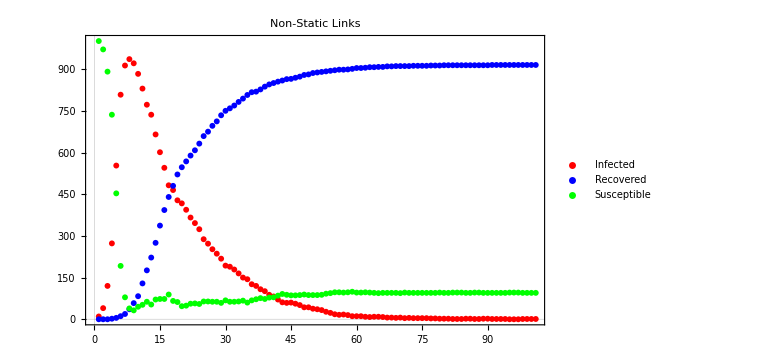

```mathematica
Agraph=AgraphInit;
pG=N[1/Ntotal];
pL=0.5;
T=10;
tmax=100;
state=Association[Apply[Sequence,Table[Rule[i,"susceptible"],{i,1,Ntotal}]]];
infectionTime=Association[Apply[Sequence,Table[Rule[i,0],{i,1,Ntotal}]]];
infectionTimeTotal=infectionTime;
connections={Count[Flatten@Agraph,1]/2};
pNL=N[1/connections[[1]]];

(*initial infection*)
initialInfectionSize=10;
init=RandomSample[Range[Ntotal],initialInfectionSize];
For[i=1,i≤initialInfectionSize,i++,
state[init[[i]]]="infected";infectionTime[init[[i]]]=1;infectionTimeTotal[init[[i]]]=RandomVariate[PoissonDistribution[T]];]
Ninfected={initialInfectionSize};Nrecovered={0};

(*time loop*)
res=Reap@Do[
stateTemp=state;
AgraphTemp=Agraph;

For[i=1,i≤Ntotal,i++,
(*increase infected time*)
If[infectionTime[i]>0,infectionTime[i]=infectionTime[i]+1];

(*if infected, infect others that are directly linked*)
If[state[i]=="infected",
For[j=1,j<Ntotal,j++
If[And[Agraph[[i,j]]>0,RandomReal[]≤pL,state[j]=="susceptible"],
stateTemp[j]="infected";
infectionTime[j]=1;
infectionTimeTotal[j]=RandomVariate[PoissonDistribution[T]];
]
]
];

(*global infection chance*)
If[And[state[i]=="susceptible",RandomReal[]≤pG],
stateTemp[i]="infected";
infectionTime[i]=1;
infectionTimeTotal[i]=RandomVariate[PoissonDistribution[T]];
];

];
state=stateTemp;

(*remove from infected with end of time*)
For[i=1,i≤Ntotal,i++,
(*increase infected time*)
If[And[state[i]=="infected",infectionTime[i]≥infectionTimeTotal[i]],
If[RandomReal[]≤0.5,
state[i]="recovered";infectionTime[i]=0;infectionTimeTotal[i]=0;,
state[i]="susceptible";infectionTime[i]=0;infectionTimeTotal[i]=0;
]
];
];

(*change links*)
For[i=1,i<Ntotal,i++,
pOL=N[10/(Ntotal-Count[Agraph[[150,All]],1])];
For[j=i+1,j< Ntotal,j++,
Which[
(*chance for a new connection*)
And[Agraph[[i,j]]==0,RandomReal[]≤pNL],
AgraphTemp[[i,j]]=1;AgraphTemp[[j,i]]=1,
(*chance that an existing link will be broken*)
And[Agraph[[i,j]]==0,RandomReal[]≤pOL],
AgraphTemp[[i,j]]=0;AgraphTemp[[j,i]]=0
];
]
];
Agraph=AgraphTemp;

(*counters*)
Sow[Count[state,"recovered"],rec];
Sow[Count[state,"infected"],inf];
Sow[Count[Flatten@Agraph,1]/2,con];
pNL=N[1/(10connections[[1]])];

,{t,tmax}];
Nrecovered=Join[Nrecovered,res[[2,1]]];
Ninfected=Join[Ninfected,res[[2,2]]];
connections=Join[connections,res[[2,3]]];
ListPlot[{Ninfected,Nrecovered,Ntotal-Ninfected-Nrecovered},PlotTheme->"Scientific",PlotStyle->{Red,Blue,Green},ImageSize->Large,PlotLegends->LineLegend[{Red,Blue,Green},{"Infected","Recovered","Susceptible"}],PlotLabel->"Non-Static Links"]
```

Once again we observe that the behavior of the system remains similar to that of the analytical SIRS model.

To continue from here we need to introduce a finer control of the creation and destruction of links that applies mostly to the communities and is not global, as set before, to introduce the appearance of persistent seeds, and also to introduce the chance of a disease’s mutation over time, making recovered individuals susceptible again.

References

```mathematica
references={
{"journal","Ball Frank, Mollison Denis, Scalia-Tomba Gianpaolo","1997","Epidemics with Two Levels of Mixing","The Annals of Applied Probability 7","46-89"},
{"journal","Ball Frank, Neal Peter","2002","A general model for stocastic SIR epidemics with two levels of mixing","Mathematica Biosciences 180","73-102"},
{"journal","Ball F., Neal P.","2004","Poisson Approximations for Epidemics with Two Levels of Mixing","The Annals of Probability 32","1168-1200"},
{"journal","Brandfor Hill, Aisting","1965","The Environment and Disease: Association or Causation?","Proceedings of Medicine 58","295-300"},
{"journal","Gandolfi Alberto, Cecconi Lorenzo","2016","SIR Epidemics on a Scale-free Spatial Nested Modual Network","Adv. Appl. Prob. 48","137-162"},
{"book","Green, David G., Lie, Jing, Abbass, Husseing A.","2014","Dual Pahse Evolution","Springer"},
{"journal","Humphries, Gurney K.","2008","Network 'small-world-ness': a quantitative method for determining canonical network equivalence","PLOT ONE 3 (4)","1-10"},
{"journal","Kim, James","","Complex Networks and Epidemiology","Center for Appled Mathematics, Institute of Sciences and Technology of Asia",""},
{"journal","Liang Che-Wei, Ku Chien-Kuo, Liang Jeng-Jong","2013","A new scale-free network model for simulating and predicting epidemics","Journal of Theoretical Biology 317","11-19"},
{"network","Lloyd Alun L., Valeika Steve","2005","Network Models in Epidemiology: An Overview",""},
{"journal","Silva S.L., Ferreira J.A., Martins M.L.","2007","Epidemic spreading in a scale-free network of regular lattices","Phys. A 377","689-697"},
{"network","Zheng Muhua, Wang Chaoqing, Zhou Jie, Zhao Ming, Guan Shuguang, Zou Yong, Liu Zonghua","2015","Non-periodic outbreaks of recurrent epidemics and its network modelling","www.nature.com/scientificreports"},
{"site","www.BMJ.com"}
};
Framed[
Column[{
TableForm[Table[{ToString[i]~~".",
Which[
references[[i,1]]=="site",Style[references[[i,2]],Italic],
references[[i,1]]=="journal",TextCell[Row[{references[[i,2]]," ("~~references[[i,3]],"); ",Style[references[[i,4]],Italic],"; ",references[[i,5]],": p. ",references[[i,6]]}]],
references[[i,1]]=="book",TextCell[Row[{references[[i,2]]," ("~~references[[i,3]],"); ",Style[references[[i,4]],Italic],"; ",references[[i,5]]}]],
references[[i,1]]=="network",TextCell[Row[{references[[i,2]]," ("~~references[[i,3]],"); ",Style[references[[i,4]],Italic],"; ",references[[i,5]]}]]
]
},{i,1,Length[references]}],TableAlignments->Left,TableSpacing->{1.25,0.3}],

Row[{
Dynamic[
ref13=Flatten[Position[references,"Ball F., Neal P."]][[1]];Spacer[0]],
Dynamic[
ref12=Flatten[Position[references,"Gandolfi Alberto, Cecconi Lorenzo"]][[1]];Spacer[0]],
Dynamic[
ref11=Flatten[Position[references,"Zheng Muhua, Wang Chaoqing, Zhou Jie, Zhao Ming, Guan Shuguang, Zou Yong, Liu Zonghua"]][[1]];Spacer[0]],
Dynamic[
ref10=Flatten[Position[references,"Lloyd Alun L., Valeika Steve"]][[1]];Spacer[0]],
Dynamic[
ref9=Flatten[Position[references,"Ball Frank, Mollison Denis, Scalia-Tomba Gianpaolo"]][[1]];Spacer[0]],
Dynamic[
ref8=Flatten[Position[references,"Silva S.L., Ferreira J.A., Martins M.L."]][[1]];Spacer[0]],
Dynamic[
ref7=Flatten[Position[references,"Liang Che-Wei, Ku Chien-Kuo, Liang Jeng-Jong"]][[1]];Spacer[0]],
Dynamic[
ref6=Flatten[Position[references,"Ball Frank, Neal Peter"]][[1]];Spacer[0]],
Dynamic[
ref5=Flatten[Position[references,"Humphries, Gurney K."]][[1]];Spacer[0]],
Dynamic[
ref4=Flatten[Position[references,"Kim, James"]][[1]];Spacer[0]],
Dynamic[
ref3=Flatten[Position[references,"Green, David G., Lie, Jing, Abbass, Husseing A."]][[1]];Spacer[0]],
Dynamic[
ref2=Flatten[Position[references,"www.BMJ.com"]][[1]];Spacer[0]],
Dynamic[
ref1=Flatten[Position[references,"Brandfor Hill, Aisting"]][[1]];Spacer[0]]
}]
},Alignment->Left]
,RoundingRadius->2,ContentPadding->False,FrameStyle->None,ImageSize->{{1,550},{1,50000}}]
```

1. | Ball Frank, Mollison Denis, Scalia-Tomba Gianpaolo (1997); Epidemics with Two Levels of Mixing; The Annals of Applied Probability 7: p. 46-89
2. | Ball Frank, Neal Peter (2002); A general model for stocastic SIR epidemics with two levels of mixing; Mathematica Biosciences 180: p. 73-102
3. | Ball F., Neal P. (2004); Poisson Approximations for Epidemics with Two Levels of Mixing; The Annals of Probability 32: p. 1168-1200
4. | Brandfor Hill, Aisting (1965); The Environment and Disease: Association or Causation?; Proceedings of Medicine 58: p. 295-300
5. | Gandolfi Alberto, Cecconi Lorenzo (2016); SIR Epidemics on a Scale-free Spatial Nested Modual Network; Adv. Appl. Prob. 48: p. 137-162
6. | Green, David G., Lie, Jing, Abbass, Husseing A. (2014); Dual Pahse Evolution; Springer
7. | Humphries, Gurney K. (2008); Network 'small-world-ness': a quantitative method for determining canonical network equivalence; PLOT ONE 3 (4): p. 1-10
8. | Kim, James (); Complex Networks and Epidemiology; Center for Appled Mathematics, Institute of Sciences and Technology of Asia: p. 
9. | Liang Che-Wei, Ku Chien-Kuo, Liang Jeng-Jong (2013); A new scale-free network model for simulating and predicting epidemics; Journal of Theoretical Biology 317: p. 11-19
10. | Lloyd Alun L., Valeika Steve (2005); Network Models in Epidemiology: An Overview; 
11. | Silva S.L., Ferreira J.A., Martins M.L. (2007); Epidemic spreading in a scale-free network of regular lattices; Phys. A 377: p. 689-697
12. | Zheng Muhua, Wang Chaoqing, Zhou Jie, Zhao Ming, Guan Shuguang, Zou Yong, Liu Zonghua (2015); Non-periodic outbreaks of recurrent epidemics and its network modelling; www.nature.com/scientificreports
13. | www.BMJ.com